```mathematica
(*Graficos de Indigenas *)

1
```

{{Estado,Procesados,Sentenciados},{OAXACA,88,102},{CHIAPAS,60,125},{NAYARIT,60,18},{SONORA,15,59},{GUERRERO,13,28},{DISTRITO FEDERAL,27,8},{CHIHUAHUA,24,8},{YUCATÁN,23,5},{ESTADO DE MÉXICO,5,17},{HIDALGO,7,11},{SINALOA,9,8},{MICHOACÁN,10,6},{PUEBLA,10,5},{BAJA CALIFORNIA,8,6},{VERACRUZ,4,8},{GUANAJUATO,10,1},{COLIMA,2,9},{MORELOS,3,7},{JALISCO,1,9},{TABASCO,8,2},{DURANGO,5,3},{CAMPECHE,0,7},{COAHUILA,6,0},{QUERÉTARO,1,2},{NUEVO LEÓN,1,0},{QUINTANA ROO,0,1},{ZACATECAS,0,1},{AGUASCALIENTES,0,0},{BAJA CALIFORNIA SUR,0,0},{SAN LUIS POTOSÍ,0,0},{TAMAULIPAS,0,0},{TLAXCALA,0,0}}

```mathematica
ndata = data[[2;;-1,{1,2}]]
```

{{OAXACA,88},{CHIAPAS,60},{NAYARIT,60},{SONORA,15},{GUERRERO,13},{DISTRITO FEDERAL,27},{CHIHUAHUA,24},{YUCATÁN,23},{ESTADO DE MÉXICO,5},{HIDALGO,7},{SINALOA,9},{MICHOACÁN,10},{PUEBLA,10},{BAJA CALIFORNIA,8},{VERACRUZ,4},{GUANAJUATO,10},{COLIMA,2},{MORELOS,3},{JALISCO,1},{TABASCO,8},{DURANGO,5},{CAMPECHE,0},{COAHUILA,6},{QUERÉTARO,1},{NUEVO LEÓN,1},{QUINTANA ROO,0},{ZACATECAS,0},{AGUASCALIENTES,0},{BAJA CALIFORNIA SUR,0},{SAN LUIS POTOSÍ,0},{TAMAULIPAS,0},{TLAXCALA,0}}

```mathematica
Length[ndata]
```

32

```mathematica
rdata = Range[Length[ndata]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32}

```mathematica
discos= Map[Disk[{#,0}, ndata[[#,2]]] &,rdata]
```

{Disk[{1,0},88],Disk[{2,0},60],Disk[{3,0},60],Disk[{4,0},15],Disk[{5,0},13],Disk[{6,0},27],Disk[{7,0},24],Disk[{8,0},23],Disk[{9,0},5],Disk[{10,0},7],Disk[{11,0},9],Disk[{12,0},10],Disk[{13,0},10],Disk[{14,0},8],Disk[{15,0},4],Disk[{16,0},10],Disk[{17,0},2],Disk[{18,0},3],Disk[{19,0},1],Disk[{20,0},8],Disk[{21,0},5],Disk[{22,0},0],Disk[{23,0},6],Disk[{24,0},1],Disk[{25,0},1],Disk[{26,0},0],Disk[{27,0},0],Disk[{28,0},0],Disk[{29,0},0],Disk[{30,0},0],Disk[{31,0},0],Disk[{32,0},0]}

```mathematica
Graphics[{EdgeForm[{Black}], Red, discos}]
```

-Graphics-

```mathematica
(* Escalo las variables  con el area para usar el radio entonces es la raiz del area*)
```

```mathematica
discos= Map[Disk[{#,0},N[Sqrt[ndata[[#,2]]]]] &,rdata]
```

{Disk[{1,0},9.38083],Disk[{2,0},7.74597],Disk[{3,0},7.74597],Disk[{4,0},3.87298],Disk[{5,0},3.60555],Disk[{6,0},5.19615],Disk[{7,0},4.89898],Disk[{8,0},4.79583],Disk[{9,0},2.23607],Disk[{10,0},2.64575],Disk[{11,0},3.],Disk[{12,0},3.16228],Disk[{13,0},3.16228],Disk[{14,0},2.82843],Disk[{15,0},2.],Disk[{16,0},3.16228],Disk[{17,0},1.41421],Disk[{18,0},1.73205],Disk[{19,0},1.],Disk[{20,0},2.82843],Disk[{21,0},2.23607],Disk[{22,0},0.],Disk[{23,0},2.44949],Disk[{24,0},1.],Disk[{25,0},1.],Disk[{26,0},0.],Disk[{27,0},0.],Disk[{28,0},0.],Disk[{29,0},0.],Disk[{30,0},0.],Disk[{31,0},0.],Disk[{32,0},0.]}

```mathematica
Graphics[{EdgeForm[{Black}], Red, discos}]
```

-Graphics-

```mathematica
(* Tomo valores de ColorBruer *)
rosa =RGBColor[250/256, 159/256,181/256]
```

-Graphics-

```mathematica
Graphics[{EdgeForm[{White}], rosa, discos}]
```

-Graphics-

```mathematica
(* Para hacer esta gráfica más pequeña *)
```

```mathematica
discos= Map[Disk[{#*10,0},N[Sqrt[ndata[[#,2]]]]*0.7] &,rdata]
```

{Disk[{10,0},6.56658],Disk[{20,0},5.42218],Disk[{30,0},5.42218],Disk[{40,0},2.71109],Disk[{50,0},2.52389],Disk[{60,0},3.63731],Disk[{70,0},3.42929],Disk[{80,0},3.35708],Disk[{90,0},1.56525],Disk[{100,0},1.85203],Disk[{110,0},2.1],Disk[{120,0},2.21359],Disk[{130,0},2.21359],Disk[{140,0},1.9799],Disk[{150,0},1.4],Disk[{160,0},2.21359],Disk[{170,0},0.989949],Disk[{180,0},1.21244],Disk[{190,0},0.7],Disk[{200,0},1.9799],Disk[{210,0},1.56525],Disk[{220,0},0.],Disk[{230,0},1.71464],Disk[{240,0},0.7],Disk[{250,0},0.7],Disk[{260,0},0.],Disk[{270,0},0.],Disk[{280,0},0.],Disk[{290,0},0.],Disk[{300,0},0.],Disk[{310,0},0.],Disk[{320,0},0.]}

```mathematica
Graphics[{EdgeForm[{Blue}], rosa, discos}]
```

-Graphics-

```mathematica
(* La cambio para que cambie de dirección horizontal a vertical - cambio x por y en la definición del disco*)

discos= Map[Disk[{0,#*10},N[Sqrt[ndata[[#,2]]]]*0.7] &,rdata]
```

{Disk[{0,10},6.56658],Disk[{0,20},5.42218],Disk[{0,30},5.42218],Disk[{0,40},2.71109],Disk[{0,50},2.52389],Disk[{0,60},3.63731],Disk[{0,70},3.42929],Disk[{0,80},3.35708],Disk[{0,90},1.56525],Disk[{0,100},1.85203],Disk[{0,110},2.1],Disk[{0,120},2.21359],Disk[{0,130},2.21359],Disk[{0,140},1.9799],Disk[{0,150},1.4],Disk[{0,160},2.21359],Disk[{0,170},0.989949],Disk[{0,180},1.21244],Disk[{0,190},0.7],Disk[{0,200},1.9799],Disk[{0,210},1.56525],Disk[{0,220},0.],Disk[{0,230},1.71464],Disk[{0,240},0.7],Disk[{0,250},0.7],Disk[{0,260},0.],Disk[{0,270},0.],Disk[{0,280},0.],Disk[{0,290},0.],Disk[{0,300},0.],Disk[{0,310},0.],Disk[{0,320},0.]}

```mathematica
Graphics[{EdgeForm[{Blue}], rosa, discos}]
```

-Graphics-

```mathematica
(* La cambio para que los circulos mas grandes estén arriba, agrego un signo - y que sea más grande con ImageSize*)
```

```mathematica
discos= Map[Disk[{0,-#*10},N[Sqrt[ndata[[#,2]]]]*0.7] &,rdata]
```

{Disk[{0,-10},6.56658],Disk[{0,-20},5.42218],Disk[{0,-30},5.42218],Disk[{0,-40},2.71109],Disk[{0,-50},2.52389],Disk[{0,-60},3.63731],Disk[{0,-70},3.42929],Disk[{0,-80},3.35708],Disk[{0,-90},1.56525],Disk[{0,-100},1.85203],Disk[{0,-110},2.1],Disk[{0,-120},2.21359],Disk[{0,-130},2.21359],Disk[{0,-140},1.9799],Disk[{0,-150},1.4],Disk[{0,-160},2.21359],Disk[{0,-170},0.989949],Disk[{0,-180},1.21244],Disk[{0,-190},0.7],Disk[{0,-200},1.9799],Disk[{0,-210},1.56525],Disk[{0,-220},0.],Disk[{0,-230},1.71464],Disk[{0,-240},0.7],Disk[{0,-250},0.7],Disk[{0,-260},0.],Disk[{0,-270},0.],Disk[{0,-280},0.],Disk[{0,-290},0.],Disk[{0,-300},0.],Disk[{0,-310},0.],Disk[{0,-320},0.]}

```mathematica
Graphics[{EdgeForm[{Black}], rosa, discos}, ImageSize->50]
```

-Graphics-

```mathematica
(* Nos regresamos a la grafica horizontal *)

discos= Map[Disk[{#*10,0},N[Sqrt[ndata[[#,2]]]]*0.7] &,rdata]
```

{Disk[{10,0},6.56658],Disk[{20,0},5.42218],Disk[{30,0},5.42218],Disk[{40,0},2.71109],Disk[{50,0},2.52389],Disk[{60,0},3.63731],Disk[{70,0},3.42929],Disk[{80,0},3.35708],Disk[{90,0},1.56525],Disk[{100,0},1.85203],Disk[{110,0},2.1],Disk[{120,0},2.21359],Disk[{130,0},2.21359],Disk[{140,0},1.9799],Disk[{150,0},1.4],Disk[{160,0},2.21359],Disk[{170,0},0.989949],Disk[{180,0},1.21244],Disk[{190,0},0.7],Disk[{200,0},1.9799],Disk[{210,0},1.56525],Disk[{220,0},0.],Disk[{230,0},1.71464],Disk[{240,0},0.7],Disk[{250,0},0.7],Disk[{260,0},0.],Disk[{270,0},0.],Disk[{280,0},0.],Disk[{290,0},0.],Disk[{300,0},0.],Disk[{310,0},0.],Disk[{320,0},0.]}

```mathematica
Graphics[{EdgeForm[{Black}], rosa, discos}, ImageSize->650]
```

-Graphics-

```mathematica
(* Agrego el dato de Sentenciados a los datos *)

ndata = data[[2;;-1,{1,2,3}]]
```

{{OAXACA,88,102},{CHIAPAS,60,125},{NAYARIT,60,18},{SONORA,15,59},{GUERRERO,13,28},{DISTRITO FEDERAL,27,8},{CHIHUAHUA,24,8},{YUCATÁN,23,5},{ESTADO DE MÉXICO,5,17},{HIDALGO,7,11},{SINALOA,9,8},{MICHOACÁN,10,6},{PUEBLA,10,5},{BAJA CALIFORNIA,8,6},{VERACRUZ,4,8},{GUANAJUATO,10,1},{COLIMA,2,9},{MORELOS,3,7},{JALISCO,1,9},{TABASCO,8,2},{DURANGO,5,3},{CAMPECHE,0,7},{COAHUILA,6,0},{QUERÉTARO,1,2},{NUEVO LEÓN,1,0},{QUINTANA ROO,0,1},{ZACATECAS,0,1},{AGUASCALIENTES,0,0},{BAJA CALIFORNIA SUR,0,0},{SAN LUIS POTOSÍ,0,0},{TAMAULIPAS,0,0},{TLAXCALA,0,0}}

```mathematica
(* Vamos a cambiar el eje Y *)
discos= Map[Disk[{#*10,ndata[[#,3]]},N[Sqrt[ndata[[#,2]]]]*0.7] &,rdata]
```

{Disk[{10,102},6.56658],Disk[{20,125},5.42218],Disk[{30,18},5.42218],Disk[{40,59},2.71109],Disk[{50,28},2.52389],Disk[{60,8},3.63731],Disk[{70,8},3.42929],Disk[{80,5},3.35708],Disk[{90,17},1.56525],Disk[{100,11},1.85203],Disk[{110,8},2.1],Disk[{120,6},2.21359],Disk[{130,5},2.21359],Disk[{140,6},1.9799],Disk[{150,8},1.4],Disk[{160,1},2.21359],Disk[{170,9},0.989949],Disk[{180,7},1.21244],Disk[{190,9},0.7],Disk[{200,2},1.9799],Disk[{210,3},1.56525],Disk[{220,7},0.],Disk[{230,0},1.71464],Disk[{240,2},0.7],Disk[{250,0},0.7],Disk[{260,1},0.],Disk[{270,1},0.],Disk[{280,0},0.],Disk[{290,0},0.],Disk[{300,0},0.],Disk[{310,0},0.],Disk[{320,0},0.]}

```mathematica
Graphics[{EdgeForm[{Black}], rosa, discos}, ImageSize->650]
```

-Graphics-

```mathematica
(*  Graficar usando codigo de barras *)
Max[ndata[[All,2]]]
```

{OAXACA,88,102}

88

```mathematica
Min[ndata[[All,2]]]
```

0

```mathematica
Max[ndata[[All,3]]]
```

125

```mathematica
Min[ndata[[All,3]]]
```

0

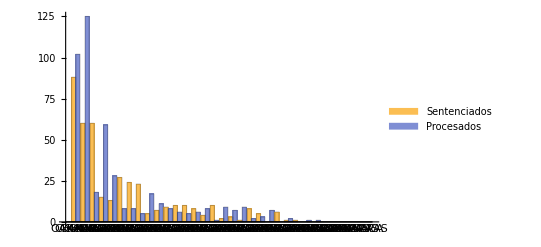

```mathematica
BarChart[ndata[[All,{2,3}]], ChartLabels ->{tdata}, ChartLegends->{"Sentenciados","Procesados"}]
```

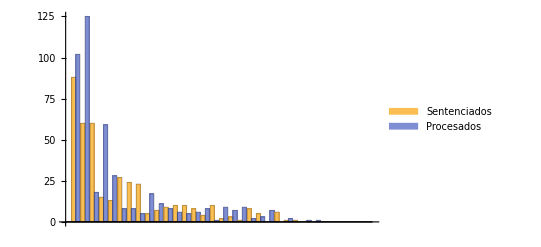

```mathematica
BarChart[ndata[[All,{2,3}]], ChartLegends->{"Sentenciados","Procesados"}]
```